√(0.5-429.245 Sin[theta]^2) (14.0689+2264.63 Sin[theta]^2-2.59222×10^6 Sin[theta]^4)

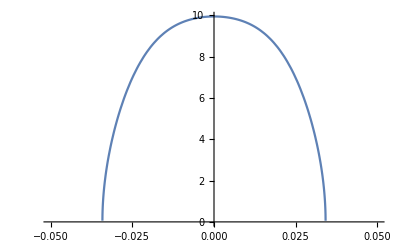

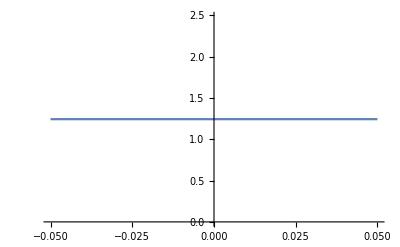

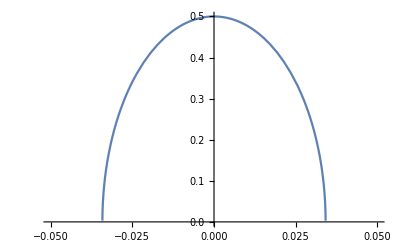

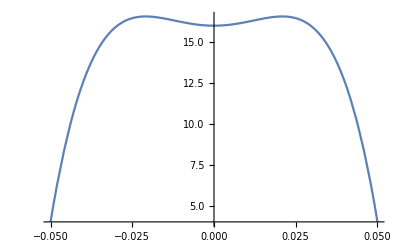

```mathematica
gamma=29.3;
lambda=0.5;
sigma = 1;
c = 1 + (gamma^2)*(Sin[theta]^2);
f1 = (2*gamma)/(15*Pi);
f2 = Sqrt[lambda*(1 - lambda*c)];
f3 = 22*c*lambda - 16*c^2*lambda^2 + 9;
F = f1*f2*f3;
FullSimplify[%]
Plot[F, {theta, -.05, .05}]
Plot[f1, {theta, -.05, .05}]
Plot[f2, {theta, -.05, .05}]
Plot[f3, {theta, -.05, .05}]
```